```mathematica
dir=NotebookDirectory[];
a=SetDirectory[dir]
date = DateString[Riffle[{"03","10"},"_"]]
```

D:\Curve Elasticity\Simulation\2026\jan\results\helicoidC\var

03_10

```mathematica
uu=Import["uu_2_26_"<>date<>".txt","Table"];
uu=Flatten[uu];
vv=Import["vv_2_26_"<>date<>".txt","Table"];
vv=Flatten[vv];

kg=Import["kg_2_26_"<>date<>".txt","Table"];
kg=Flatten[kg];
kn=Import["kn1_2_26_"<>date<>".txt","Table"];
kn=Flatten[kn];

taug=Import["taug_2_26_"<>date<>".txt","Table"];
taug=Flatten[taug];
phi=Import["phi_2_26_"<>date<>".txt","Table"];
phi=Flatten[phi];

l1=Import["l1_2_26_"<>date<>".txt","Table"];
l1=Flatten[l1];
```

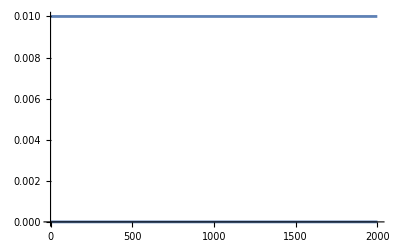

```mathematica
a1=ListLinePlot[{l1}];
a2=Plot[10^(-2),{x,0,2000}];
Show[a1,a2,PlotRange->All]
```